## Evaluating Higher-Order Moments for Ordinary Least-Squares Estimators Author: Graham Van Goffrier, Tech Research, Spotify July - September 2022

The purpose of this notebook is to evaluate obtain closed-form or at least compact numerical expressions for quadratic and higher-order moments of estimators constructed by ordinary least-squares (OLS) principles. All linear moments and many quadratic moments may be explicitly evaluated (in the case of multivariate normal random variables) using tools such as the Law of Total Expectation/Covariance, as demonstrated in [Gupta2021], and projection of multivariate normal distributions onto conditional expectations, as detailed in the preceding notebook “Estimating Treatment Effects with Fuzzy Mediators”.

First, we perform a numerical study of the expectation value E[(A.M)^2/(A^2 M^2)], where A and M have a bivariate normal distribution. If A and M are taken to be independent, this reduces to E[cos^2 θ] = 1/n where n is the number of samples, but covariance between A and M complicates matters. IN PROGRESS

Next, we consider slight generalizations to the quadratic expectation such as E[((A.M)(B.M))/M^2], where B is independent of bivariate normal (A,M), or more generally where (A,B,M) are trivariate normal. INCOMPLETE

Next, we will attempt to extend the above results to cubic and higher-order expectations, taking advantage of the Law of Total Covariance and the cumulant-moment reduction relations for multivariate normal distributions to absorb all terms of order higher than quadratic. INCOMPLETE

The overarching goal is for any expression of the form E[(∑β_ij X_i.X_j + ∑β_ijkl X_i.X_jX_k.X_l + ...)/(∑α_ij X_i.X_j + ∑α_ijkl X_i.X_jX_k.X_l + ...)], where α_ij,β_ij,etc. ∈ ℝ, and X_i are vectors of distribution samples drawn from multivariate (normal) distribution Ν(μ⃗,Σ), to be at best analytically known or at worst expressible in terms of known numerical integrals which can be quickly evaluated.

### E[(A.M)^2/(A^2 M^2)]: the independent case

Suppose A and M are independent n-dimensional vectors, selected from some probability distribution which is radially symmetric on the (n-1)-sphere. Then 
E[(A.M)^2/(A^2 M^2)]=E[cos^2 θ]=(∫_0)^π dθ (sin(θ))^n(cos(θ))^2=1/(n+2).
In the above, the magnitudes of A and M are irrelevant -- note that this does not mean we could cleanly evaluate E[(A.M)^2], which would go as ∫dr_A dr_M r_A^4

{π,2,π/2,4/3,(3 π)/8,16/15,(5 π)/16,32/35,(35 π)/128,256/315,(63 π)/256,512/693,(231 π)/1024,2048/3003,(429 π)/2048,4096/6435,(6435 π)/32768,65536/109395,(12155 π)/65536,131072/230945,(46189 π)/262144}

{π/2,2/3,π/8,4/15,π/16,16/105,(5 π)/128,32/315,(7 π)/256,256/3465,(21 π)/1024,512/9009,(33 π)/2048,2048/45045,(429 π)/32768,4096/109395,(715 π)/65536,65536/2078505,(2431 π)/262144,131072/4849845,(4199 π)/524288}

{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22}

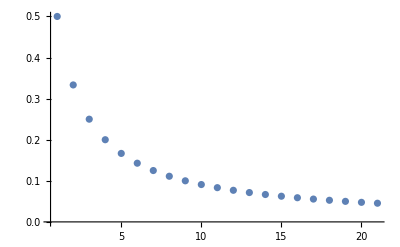

```mathematica
norms=Table[Integrate[Sin[x]^n,{x,0,π}],{n,0,20}]
vals=Table[Integrate[Sin[x]^n*Cos[x]^2,{x,0,π}],{n,0,20}]
normvals=MapThread[#1/#2&,{vals,norms}]
ListPlot[normvals,PlotRange->All]
```

If we impose the true causal dependence M = cX + uM, the expectation value can be reduced geometrically to the following integral, where X is the magnitude of sample vector X (rotated by symmetry to the ẑ direction), Z is the z-component of sample vector uM, and R is the radial component of uM in cylindrical coordinates about z. A constant factor on the front will depend on the dimensionality n of the sample vectors, but by symmetry the integral itself is three-dimensional:

```mathematica
stringifySubs={Subscript[var_,sub__]:>Subscript[var,ToString[sub]]};
cos2integrand[Cx_,X_,R_,Z_]:=R*X^2(Cx*X+Z)^2/((Cx*X+Z)^2+R^2)Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)]/.stringifySubs;
cos2int=Defer[Integrate[R*X^2(Cx*X+Z)^2/((Cx*X+Z)^2+R^2)Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)],{X,0,∞},{R,0,∞},{Z,0,∞}]]
```

∫_0^∞ ∫_0^∞ ∫_0^∞ (R X^2 (Cx X+Z)^2 Exp[-X^2/(2 σ_X^2)-(R^2+Z^2)/(2 σ_uM^2)])/((Cx X+Z)^2+R^2)ⅆZⅆRⅆX

```mathematica
cos2integrand/.stringifySubs/.{X->X*Subscript[σ, "X"],R->R*Subscript[σ, "uM"],Z->Z*Subscript[σ, "uM"]}//Simplify
```

cos2integrand

```mathematica
fixConsts={Subscript[σ, X]->1,Subscript[σ, uM]->2};
top=Infinity;
CxMax=10;
CxStep=0.5;
normXM=NIntegrate[R^1*X^2 Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)]/.fixConsts,{X,0,top},{R,0,top},{Z,0,top}];
expcos2XM=Table[NIntegrate[R^1 X^2(Cx*X+Z)^2/((Cx*X+Z)^2+R^2)Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)]/.fixConsts,{X,0,top},{R,0,top},{Z,0,top}],{Cx,-1*CxMax,CxMax,CxStep}];
normExpCos2XM=expcos2XM/normXM;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

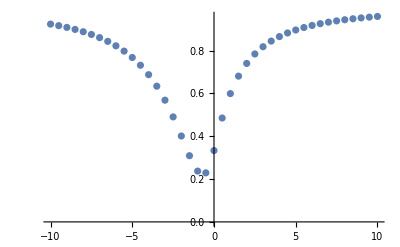

```mathematica
ListPlot[Transpose@{Range[-1*CxMax,CxMax,CxStep],normExpCos2XM},PlotRange->All]
```

One pathway to simplification is to find a suitable series expansion. For example, we could expand in R:

```mathematica
Series[(X+Z)^2/((X+Z)^2+R^2),{R,0,10}]//Simplify
```

1-R^2/(X+Z)^2+R^4/(X+Z)^4-R^6/(X+Z)^6+R^8/(X+Z)^8-R^10/(X+Z)^10+O[R]^11

and then solve the R integral exactly for each term:

```mathematica
A[n_,K_]=Integrate[R^n Exp[R^2/(-2K)],{R,0,∞}]
A[2,K]
```

ConditionalExpression[2^(1/2 (-1+n)) K^((1+n)/2) Gamma[(1+n)/2], Re[K]>0&&Re[n]>-1]

ConditionalExpression[K^(3/2) √(π/2), Re[K]>0]

Defining the above series as A[n], we now have 

∫dXdZdR R^4 X^5(Cx*X+Z)^2/((Cx*X+Z)^2+R^2)Exp[-X^2/(2 σ_X^2)-(R^2+Z^2)/(2 σ_uM^2)] =(Σ_(n=0))^∞A[2n+4,σ_uM^2](-1)^n∫dXdZ X^5/(Cx*X+Z)^(2n)Exp[-X^2/(2 σ_X^2)-Z^2/(2 σ_uM^2)]
To expand further, we can expand in X and absorb the numerator

```mathematica
Series[1/(X+Z)^2,{X,0,10}]//Simplify
Series[1/(X+Z)^3,{X,0,10}]//Simplify
```

1/Z^2-(2 X)/Z^3+(3 X^2)/Z^4-(4 X^3)/Z^5+(5 X^4)/Z^6-(6 X^5)/Z^7+(7 X^6)/Z^8-(8 X^7)/Z^9+(9 X^8)/Z^10-(10 X^9)/Z^11+(11 X^10)/Z^12+O[X]^11

1/Z^3-(3 X)/Z^4+(6 X^2)/Z^5-(10 X^3)/Z^6+(15 X^4)/Z^7-(21 X^5)/Z^8+(28 X^6)/Z^9-(36 X^7)/Z^10+(45 X^8)/Z^11-(55 X^9)/Z^12+(66 X^10)/Z^13+O[X]^11

where the general expression is 1/(X+Z)^N=1/Z^N((Σ^∞)_(m=0)(-1))^m Binomial[m+N, N](X/Z)^m.
So, ∫dXdZ X^5/(Cx*X+Z)^(2n)Exp[-X^2/(2 σ_X^2)-Z^2/(2 σ_uM^2)]
= (Σ_(m=0))^∞A[m+5,σ_X^2](-Cx)^m Binomial[m+2n, 2n]∫dZ 1/Z^(2n+m)Exp[-Z^2/(2 σ_uM^2)]

Individual integrals of the type ∫dZ 1/Z^k Exp[-Z^2/(2 σ_uM^2)] for k>0 do not converge, but we can expect that the full resummed integral will converge for all values of n and Cx (since 1/(1+Z)^NExp[-Z^2] converges, see Integrate[(R+1)^-N Exp[R^2/-2],{R,0,∞}], and ... ). Therefore we should consider:
∫dXdZ X^5/(Cx*X+Z)^(2n)Exp[-X^2/(2 σ_X^2)-Z^2/(2 σ_uM^2)]=∫dZ(Σ_(m=0))^∞A[m+5,σ_X^2](-Cx)^m Binomial[m+2n, 2n]1/Z^(2n+m)Exp[-Z^2/(2 σ_uM^2)]
I will assess this numerically below, setting σ_uM^2=σ_X^2=1 for simplicity (this should not affect convergence).

```mathematica
cosint2d[n_,Cx_]=NIntegrate[X^5/(Cx*X+Z)^(2n)Exp[-X^2/(2 Subscript[σ, X]^2)-Z^2/(2 Subscript[σ, uM]^2)]/.fixConsts,{X,0,top},{Z,0,top}];
cosint2d[10,1]
```

NIntegrate::inumr: The integrand ⅇ^(-X^2/2-Z^2/8) X^5 (Cx X+Z)^(-2 n) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.},{∞,0.}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::zeroregion: Integration region {{0,0},{0,0}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in X near {X,Z} = {2.5908505665283333876159055588401198713348001093308844155071110411×10^-77,0}. NIntegrate obtained 1.6059173663096025017697908077823099414352835728192055380910223947×10^997 and 1.3971315197608334446779951615360661908687288495185198590984283068×10^995 for the integral and error estimates.

1.6059173663096×10^997

```mathematica
IntZ[m_,n_,C_,z_]:=A[m+5,1](-C)^m Binomial[m+2n,2n]*z^(-2n-m)Exp[-z^2/2]
ResumIntZ[n_,C_,z_]:=Sum[IntZ[m,n,C,z],{m,0,100}]
IntZ[100,1,1,1]
```

1871111709495516523857241922944849818080727419499714148268792231388254306304000000000000/(√ⅇ)

```mathematica
Integrate[(R)^-1 Exp[R^2/-2],{R,0,∞}]
```

Integrate::idiv: Integral of (ⅇ^(-R^2/2))/R does not converge on {0,∞}.

∫_0^∞ (ⅇ^(-R^2/2))/R ⅆR

```mathematica
Series[(X+Z)^2/((X+Z)^2+R^2),{Z,0,10}]//Simplify
Integrate[Z^n Exp[Z^2/-2],{Z,0,∞}]
```

X^2/(R^2+X^2)+(2 R^2 X Z)/((R^2+X^2)^2)+((R^4-3 R^2 X^2) Z^2)/((R^2+X^2)^3)+(4 R^2 X (-R^2+X^2) Z^3)/((R^2+X^2)^4)-(R^2 (R^4-10 R^2 X^2+5 X^4) Z^4)/((R^2+X^2)^5)+((6 R^6 X-20 R^4 X^3+6 R^2 X^5) Z^5)/((R^2+X^2)^6)+((R^8-21 R^6 X^2+35 R^4 X^4-7 R^2 X^6) Z^6)/((R^2+X^2)^7)+(8 (-R^8 X+7 R^6 X^3-7 R^4 X^5+R^2 X^7) Z^7)/((R^2+X^2)^8)-(R^2 (R^8-36 R^6 X^2+126 R^4 X^4-84 R^2 X^6+9 X^8) Z^8)/((R^2+X^2)^9)+(2 R^2 X (5 R^8-60 R^6 X^2+126 R^4 X^4-60 R^2 X^6+5 X^8) Z^9)/((R^2+X^2)^10)+(R^2 (R^10-55 R^8 X^2+330 R^6 X^4-462 R^4 X^6+165 R^2 X^8-11 X^10) Z^10)/((R^2+X^2)^11)+O[Z]^11

ConditionalExpression[2^(1/2 (-1+n)) Gamma[(1+n)/2], Re[n]>-1]

```mathematica
Simplify[Integrate[R*X^2 Exp[-X^2/2-R^2/2],{Z,0,∞}],Assumptions->{{X,R}∈Reals}]
```

Integrate::idiv: Integral of ⅇ^(-R^2/2-X^2/2) R X^2 does not converge on {0,∞}.

Integrate::idiv: Integral of 1 does not converge on {0,∞}.

ⅇ^(-R^2/2-X^2/2) R X^2 ∫_0^∞ 1ⅆZ

Armed with the knowledge of the above divergent series, we can now attempt to improve on this procedure by trying to circumvent the rapidly-varying regions of the integrand. First, we integrate directly over R, which from the first series expansion must be possible:

```mathematica
cos2intXZ=Integrate[R^1*X^2(Cx*X+Z)^2/((Cx*X+Z)^2+R^2)Exp[-X^2/(2 Subscript[σ, X]^2)-(R^2+Z^2)/(2 Subscript[σ, uM]^2)],{R,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(1/2 X ((Cx (Cx X+2 Z))/σ_uM^2-X/σ_X^2)) X^2 (Cx X+Z)^2 (Gamma[0,(Cx X+Z)^2/(2 σ_uM^2)]+Log[1/(Cx X+Z)^2]-Log[1/σ_uM^2]+Log[(Cx X+Z)^2/σ_uM^2]), ]

1/2 ⅇ^(1/2 X (-X+1/4 Cx (Cx X+2 Z))) X^2 (Cx X+Z)^2 (Gamma[0,1/8 (Cx X+Z)^2]+Log[4]+Log[1/(Cx X+Z)^2]+Log[1/4 (Cx X+Z)^2])

2

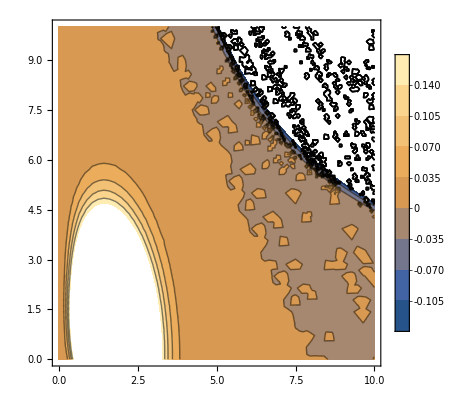

1.10307

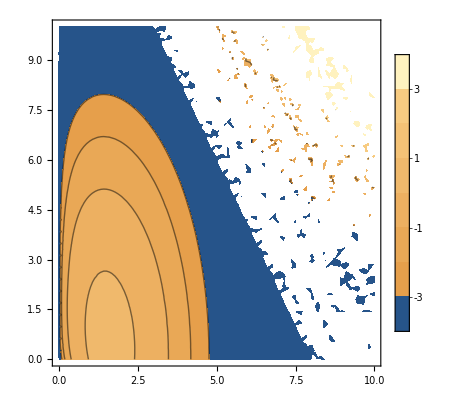

```mathematica
cos2intXZ=1/2 ⅇ^(1/2 X ((Cx (Cx X+2 Z))/Subscript[σ, uM]^2-X/Subscript[σ, X]^2)) X^2 (Cx X+Z)^2 (Gamma[0,(Cx X+Z)^2/(2 Subscript[σ, uM]^2)]+Log[1/(Cx X+Z)^2]-Log[1/Subscript[σ, uM]^2]+Log[(Cx X+Z)^2/Subscript[σ, uM]^2]);
cos2intXZ/.fixConsts
thiscx=2
ContourPlot[cos2intXZ/.fixConsts/.{Cx->thiscx},{X,0,10},{Z,0,10},Contours->10,PlotLegends->Automatic]
cos2intXZ/.fixConsts/.{Cx->thiscx}/.{X->2.0,Z->2.0}//Evaluate
ContourPlot[Log10[cos2intXZ]/.fixConsts/.{Cx->thiscx},{X,0,10},{Z,0,10},Contours->{-3,-2,-1,0,1,2,3},PlotLegends->Automatic]
```

```mathematica
LogIncompleteGamma=1
```

```mathematica
thiscx=1.0``100;
thisX=6.0``100;
thisZ=6.0``100;
cos2intXZ/.fixConsts/.{Cx->thiscx}/.{X->thisX,Z->thisZ}
Log10[1/2 ⅇ^(1/2 X ((Cx (Cx X+2 Z))/Subscript[σ, uM]^2-X/Subscript[σ, X]^2)) X^2 (Cx X+Z)^2] /.fixConsts/.{Cx->thiscx}/.{X->thisX,Z->thisZ}
N[(Gamma[0,(Cx X+Z)^2/(2 Subscript[σ, uM]^2)]+Log[1/(Cx X+Z)^2]-Log[1/Subscript[σ, uM]^2]+Log[(Cx X+Z)^2/Subscript[σ, uM]^2])/.fixConsts/.{Cx->thiscx}/.{X->thisX,Z->thisZ},20]
```

2.313953563378572946715333468887951602900025564913761172281371313126663410859898654×10^-8

1.4593098286339225008187259515182035003166783379568266183565578426100666360668485533249974111584532

8.0360903448286776572×10^-10

```mathematica
Integrate[1/2 ⅇ^(1/2 X ((Cx (Cx X+2 Z))/Subscript[σ, uM]^2-X/Subscript[σ, X]^2)) X^2 (Cx X+Z)^2,{Z,0,∞}]
```

ConditionalExpression[-(ⅇ^(1/2 X^2 (Cx^2/σ_uM^2-1/σ_X^2)) σ_uM^2 (Cx^4 X^4-2 Cx^2 X^2 σ_uM^2+2 σ_uM^4))/(2 Cx^3 X), Re[(Cx X)/σ_uM^2]<0]

```mathematica
cos2intXZ/.fixConsts/.{Cx->1.0``100}
```

1/2 ⅇ^(1/2 X (-X+0.25 (1. X+2 Z))) X^2 (1. X+Z)^2 (Gamma[0,1/8 (1. X+Z)^2]+Log[4]+Log[1/(1. X+Z)^2]+Log[1/4 (1. X+Z)^2])

```mathematica
top=1

NIntegrate[cos2intXZ/.fixConsts/.{Cx->1},{X,0,top},{Z,0,top}]
```

1

0.269659

```mathematica
top=10;
CxMax=5.0``200;
CxStep=0.1``200;
expcos2XMfromR=Table[NIntegrate[cos2intXZ/.fixConsts,{X,0,top},{Z,0,top},WorkingPrecision->15],{Cx,-1*CxMax,CxMax,CxStep}];
normExpCos2XMfromR=expcos2XMfromR/normXM
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.768082,0.761396,0.754446,0.747221,0.739706,0.731891,0.723759,0.7153,0.706497,0.697336,0.687801,0.677893,0.667566,0.656818,0.645636,0.634004,0.621906,0.609331,0.596264,0.582696,0.568619,0.554026,0.538915,0.523289,0.507157,0.490533,0.473442,0.455916,0.438001,0.419759,0.401264,0.382615,0.36393,0.345353,0.32706,0.309255,0.29218,0.276113,0.261372,0.248314,0.237332,0.228856,0.223338,0.221249,0.223055,0.229204,0.240084,0.255989,0.277039,0.303067,0.333333,0.365595,0.39757,0.428393,0.457694,0.485333,0.511283,0.535585,0.558309,0.579546,0.59939,0.617938,0.635285,0.651518,0.666723,0.680977,0.694353,0.706917,0.718731,0.72985,0.740327,0.750208,0.759537,0.768353,0.776692,0.78458,0.792067,0.799138,0.805836,0.812128,0.818111,0.823794,0.828971,0.833756,0.838385,0.842598,0.846535,0.849716,0.852289,0.856701,0.857777,0.859527,0.860612,0.859569,0.863114,0.859014,0.861511,0.857256,0.85357,0.8526}

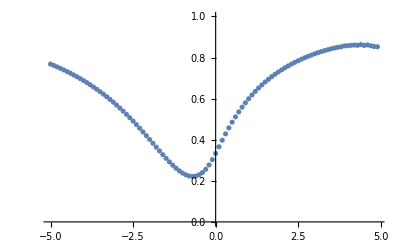

```mathematica
ListPlot[Transpose@{Range[-1*CxMax,CxMax,CxStep],normExpCos2XMfromR},PlotRange->{0,1}]
```

Another direction is to apply the Cauchy-Schwarz Inequality: E[(X.M)^2/(X^2 M^2)] ≤√(E[(X.M)/X^2]E[(X.M)/M^2])= √(F_XM F_MX), establishing an explicit upper bound on the covariance (which is positive by the positivity of both components of (X.M)^2/(X^2 M^2).

```mathematica
noisenames={"X"};
noises=Map[Symbol,noisenames];
condmeanXonM=CondMeans[causalgraph,noisenames,{"M"}][[1]];
noisenames={"M"};
noises=Map[Symbol,noisenames];
condmeanMonX=CondMeans[causalgraph,noisenames,{"X"}][[1]];
CSUpperBound=Sqrt[condmeanMonX*condmeanXonM/(X*M)]//Simplify
```

√(causalgraph^2/(M X))

```mathematica
covestimateterms=covestimatesimp/.stringifySubs/.{uM->M-c*X}//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Expand
covtermslist=List@@covestimateterms;
```

covestimatesimp

```mathematica
covExact=(covtermslist[[1]]/.{X->condmeanXonM}) + covtermslist[[2]]+covtermslist[[3]]+(covtermslist[[4]]/.{M->condmeanMonX})/.stringifySubs//TensorExpand[#,Assumptions->{vweights ∈Reals,{a,b,c,d}∈Reals}]&//Expand
```

Part::partd: Part specification covestimatesimp⟦1⟧ is longer than depth of object.

Part::partd: Part specification covestimatesimp⟦2⟧ is longer than depth of object.

Part::partd: Part specification covestimatesimp⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

covestimatesimp⟦1⟧+covestimatesimp⟦2⟧+covestimatesimp⟦3⟧+covestimatesimp⟦4⟧